```mathematica
Dma[ n_, k_, a_, s_] := Sum[ (j+a)^-s Dma[ n (j+a)^-1,k-1, a, s], {j,1,n}]; Dma[n_,0,a_,s_] := UnitStep[n-1]
Dma2[n_, k_, a_, s_] := Sum[ Binomial[k,j] Dma[n/(a+1)^(k-j),j,a+1,s],{j,0,k}]
Dma3[n_, k_, a_, s_] := Sum[ (-1)^(k-j) Binomial[k,j] Dma[n/a^(k-j),j,a-1,s],{j,0,k}]
```

```mathematica
Dma[100,2,2.31,0]
```

159.

```mathematica
Dma2[100,2,2.31,0]
```

159.

```mathematica
Dma3[100,2,2.31,0]
```

159.

```mathematica
Dp1[ n_, k_, s_] := Dp1[ n, k-1,s] + Sum[ j^-s Dp1[n j^-1,k-1,s],{j,1,n}]; Dp1[n_, 0, s_] := UnitStep[n-1]
Dk[ n_, k_, s_] := Sum[ j^-s Dk[n j^-1,k-1,s],{j,1,n}]; Dk[n_, 0, s_] := UnitStep[n-1]
Dp1a[ n_, k_, s_] := Sum[ Binomial[ k,j] Dk[ n, j,s],{j,0,k}]
```

```mathematica
E1ab1[n_,k_, x_,s_]:= Sum[j^(-s) E1ab1[n/j,k-1,x,s]-x (j x)^(-s) E1ab1[n/(x j),k-1,x,s],{j,1,n}];E1ab1[n_,0,a_,s_]:=UnitStep[n-1]
E1ab2[n_,k_, x_,s_]:= Sum[j^(-s) E1ab2[n/j,k-1,x,s]-x (j x)^(-s) E1ab2[n/(x j),k-1,x,s],{j,1,n}];E1ab2[n_,0,a_,s_]:=UnitStep[n-1]
```

```mathematica
(1/4)Sum[ 1, {x,1,40},{y,1,40/x}]
```

79/2

```mathematica
f1[n_, a_,s_] := a^(-2(s-1))Sum[ x^-s y^-s, {x,1,Floor[n a^-2]},{y,1,Floor[a^-2 n/x]}]
 f2[n_, a_,s_] := Sum[ a^2 x^-s y^-s,{x,a,n/a,a},{y,a,n/x,a}]
```

```mathematica
f1[20,1/3,-2]
```

11960423/729

```mathematica
f2[20,1/3,-2]
```

11960423/729

```mathematica
(1/2)^(2(1 -(-1)))
```

1/16

```mathematica
ds[ n_, k_, y_,s_] := y^(1-s)Sum[ j^-s ds[ n (j y )^-1,k-1, y,s],{j,1, n y }]; ds[n_, 0, y_,s_] := UnitStep[n-1]
```

```mathematica
ds[100,2,1/10,0]
```

291/100

```mathematica
f[n_,j_] := 1-j(Floor[n/j]-Floor[(n-1)/j])
```

```mathematica
N[Sum[ f[k,2400]/k,{k,1,2400}]]
```

7.36065

```mathematica
f[3,3]
```

-2

```mathematica
N[Log[1200]]
```

7.09008

```mathematica
N[ Sum[ 1/j,{j,1,2400}]]
```

8.36065

```mathematica
N[HarmonicNumber[s]-(HarmonicNumber[ 90000 ] - HarmonicNumber[Floor[90000/s]])]/.s->400
```

0.58068

```mathematica
N[Log[3]]
```

1.09861

```mathematica
N[HarmonicNumber[ 900000 ] - HarmonicNumber[900000/5000]]
```

8.51442

```mathematica
Log[5000.]
```

8.51719

```mathematica
{Limit[(y^(s-1) HurwitzZeta[s,y+1])^k,y->Infinity],1/(s-1)^k}
```

{(1/(-1+s))^k,(-1+s)^-k}

```mathematica
{Limit[(y^(1-s) HurwitzZeta[s,1/y+1])^k,y->0],1/(s-1)^k}
```

{(1/(-1+s))^k,(-1+s)^-k}

```mathematica
Grid[Table[Chop[N[1/((s-1)^k)+Integrate[D[(Zeta[s,1/y+1]y^(1-s))^k,y],{y,0,1}]]-N[(Zeta[s]-1)^k]],{s,2,4},{k,1,4}]]
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

```mathematica
Grid[Table[Chop[N[1/((s-1)^k)-Integrate[D[(Zeta[s,y+1]y^(s-1))^k,y],{y,1,Infinity}]]-N[(Zeta[s]-1)^k]],{s,2,4},{k,1,4}]]
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

```mathematica
Grid[Table[N[Integrate[D[(Zeta[s,1/y+1]y^(1-s))^k,y],{y,0,1}]],{s,2,4},{k,1,4}]]
```

-0.355066 | -0.58406 | -0.731746 | -0.826994
-0.297943 | -0.209173 | -0.116751 | -0.0608332
-0.25101 | -0.104334 | -0.0364791 | -0.0122997

```mathematica
Grid[Table[N[Integrate[D[(Zeta[s,y+1]y^(s-1))^k,y],{y,1,Infinity}]],{s,2,4},{k,1,4}]]
```

0.355066 | 0.58406 | 0.731746 | 0.826994
0.297943 | 0.209173 | 0.116751 | 0.0608332
0.25101 | 0.104334 | 0.0364791 | 0.0122997

```mathematica
{Limit[(y^(1-s) HurwitzZeta[s,y^-1+1])^k,y->0],1/(s-1)^k}
```

{(1/(-1+s))^k,(-1+s)^-k}

```mathematica
Grid[Table[Chop[N[1/((s-1)^k)+Integrate[D[(Zeta[s,y^-1+1]y^(1-s))^k,y],{y,0,1}]]-N[(Zeta[s]-1)^k]],{s,2,4},{k,1,4}]]
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

```mathematica
Table[{Zeta[s]-1,1/(s-1)-Integrate[D[y^(s-1) Zeta[s,y+1],y],{y,1,Infinity}]},{s,2,6}]
```

{{-1+π^2/6,-1+π^2/6},{-1+Zeta[3],-1+Zeta[3]},{-1+π^4/90,-1+π^4/90},{-1+Zeta[5],-1+Zeta[5]},{-1+π^6/945,-1+π^6/945}}

```mathematica
Table[-Integrate[D[y^(s-1) Zeta[s,y+1],y],{y,1,Infinity}],{s,2,6}]
```

{-2+π^2/6,-3/2+Zeta[3],-4/3+π^4/90,-5/4+Zeta[5],-6/5+π^6/945}

```mathematica
Table[Integrate[D[y^(1-s) Zeta[s,y^-1+1],y],{y,0,1}],{s,2,6}]
```

{∫_0^1 (-Zeta[2,1+1/y]/y^2+(2 Zeta[3,1+1/y])/y^3)ⅆy,∫_0^1 (-(2 Zeta[3,1+1/y])/y^3+(3 Zeta[4,1+1/y])/y^4)ⅆy,∫_0^1 (-(3 Zeta[4,1+1/y])/y^4+(4 Zeta[5,1+1/y])/y^5)ⅆy,∫_0^1 (-(4 Zeta[5,1+1/y])/y^5+(5 Zeta[6,1+1/y])/y^6)ⅆy,∫_0^1 (-(5 Zeta[6,1+1/y])/y^6+(6 Zeta[7,1+1/y])/y^7)ⅆy}

```mathematica
Grid[Table[Chop[N[1/((s-1)^k)+Integrate[D[(Zeta[s,y^-1+1]y^(1-s))^k,y],{y,0,1}]]-N[(Zeta[s]-1)^k]],{s,2,4},{k,1,4}]]
```

0.355066 | 0.58406 | 0.731746 | 0.826994
0.375 | 0.215111 | 0.117208 | 0.0608684
0.270833 | 0.104727 | 0.0364869 | 0.0122999

```mathematica
{Limit[y^(1-s) HurwitzZeta[s,y^-1+1],y->0],1/(s-1)}
```

{1/(-1+s),1/(-1+s)}

```mathematica
{Limit[y^(s-1) HurwitzZeta[s,y+1],y->Infinity],1/(s-1)}
```

{1/(-1+s),1/(-1+s)}

```mathematica
Integrate[ y^s,{y,0,1}]
```

ConditionalExpression[1/(1+s),Re[s]>-1]

```mathematica
N[Gamma[3,0,(s-1)Log[x]]/Gamma[3]/.{x->100000,s->11}]
```

1.

```mathematica
(Zeta[s,y^-1+1]y^(1-s)+1)^z-FullSimplify[Sum[Binomial[z,k](Zeta[s,y^-1+1]y^(1-s))^k,{k,0,Infinity}]]
```

0

```mathematica
D1y1[x_,s_,k_,y_]:=D1y1[x,s,k,y]=D1y1[x,s,k-1,y]+y Sum[(1+j y)^-s D1y1[x (1+j y)^-1,s,k-1,y],{j,1,(x-1)/y}];D1y1[x_,s_,0,y_]:=UnitStep[x-1]
```

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Da[ n_, k_, a_, s_] := Da[n,k,a,s]=Sum[ (j+a)^-s Da[ n/(j+a), k-1,a,s],{j,1,n-a}]; Da[n_, 0, a_, s_] := UnitStep[n-1]
Daz[n_, z_, a_, s_] := Sum[ bin[ z,k] Da[n,k,a-1,s],{k,0,Log[a,n]}]
```

```mathematica
D[N[Limit[(Daz[100,z,2,s]-1)/z,z->0]],s]/.s->0
```

-94.0453

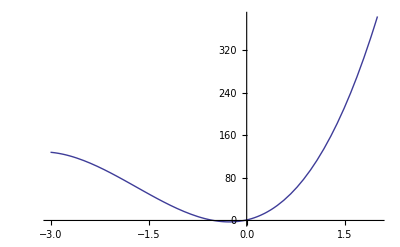

```mathematica
Plot[Re[Daz[100,z,3,0]],{z,-3,2}]
```

```mathematica
DiscretePlot[-D[Limit[(Daz[n,z,2,s]-1)/z,z->0],s]/.s->0,{n,2,100}]
```

$Aborted

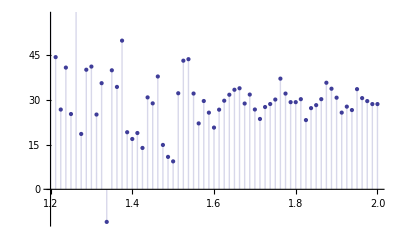

```mathematica
DiscretePlot[Limit[(Daz[100,z,a,0]-1)/z,z->0],{a,1.2, 2, .0125}]
```

```mathematica
Expand[Daz[100,z,3,0]]
```

1+(341 z)/12+(1391 z^2)/24+(139 z^3)/12+z^4/24

```mathematica
FullSimplify[D[1/(s-1)^k(Gamma[k,0,(s-1)Log[n]]/Gamma[k]),s]/.s->0]
```

((-1)^-k (k Gamma[k,0,-Log[n]]-n (-Log[n])^k))/Gamma[k]

```mathematica
1/(s-1)^k(Gamma[k,0,(s-1)Log[n]]/Gamma[k])
```

((-1+s)^-k Gamma[k,0,(-1+s) Log[n]])/Gamma[k]

```mathematica
FullSimplify[Table[ Zeta[s,a]^k-Sum[(a^-s)^(k-j)Binomial[k,j] Zeta[s, a+1]^j, {j,0,k}],{k,1,5},{a,2,5},{s,2,4}]]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
FullSimplify[Zeta[s,a]-Zeta[s,a+1]]/.{s->3,a->3}
```

```mathematica
N[Zeta[3,3]-Zeta[3,4]]
```

0.037037

```mathematica
N[3^-3]
```

0.037037

```mathematica
(a^-s)
```

```mathematica
FullSimplify[Table[ Zeta[s,a]^k-Sum[a^(-s(k-j))Binomial[k,j] Zeta[s, a+1]^j, {j,0,k}],{k,1,5},{a,2,5},{s,2,4}]]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
N[Table[ Zeta[s,a]^k-Sum[a^(-s(j))Binomial[k,j] Zeta[s, a+1]^(k-j), {j,0,k}],{k,2,3},{a,2,3},{s,2,3}]]
```

{{{0.,-2.08167×10^-17},{2.77556×10^-17,8.67362×10^-19}},{{-2.77556×10^-17,-6.50521×10^-18},{2.77556×10^-17,5.42101×10^-20}}}

```mathematica
N[Table[ Zeta[s,a]^k-Sum[(-1)^(k-j) (a-1)^(-s j)Binomial[k,j] Zeta[s, a-1]^(k-j), {j,0,k}],{k,2,3},{a,4,6},{s,2,3}]]
```

{{{-2.77556×10^-17,-8.67362×10^-19},{0.,-2.1684×10^-19},{-1.38778×10^-17,1.0842×10^-19}},{{0.045727,0.000128191},{0.0216825,0.0000290352},{0.0119231,8.81361×10^-6}}}

```mathematica
FullSimplify[Table[ Zeta[s,a]^k-Sum[(-1)^(k-j) (a-1)^(-s(k-j))Binomial[k,j] Zeta[s, a-1]^j, {j,0,k}],{k,1,5},{a,2,5},{s,2,4}]]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
FullSimplify[Table[ Chop[Zeta[s,a]^z-Sum[(-1)^j (a-1)^(-s j)Binomial[z,j] Zeta[s, a-1]^(z-j), {j,0,Infinity}]],{z,2.5,5, .7},{a,2,5},{s,2,4}]]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
dz[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Dz[n_,z_]:=Sum[dz[j,z],{j,1,n}]
D2z[n_, z_,t_] := Sum[(-1)^j  Binomial[z,j]Dz[n,z-j], {j,0,t}]
```

```mathematica
Table[ D2z[100,2.5,j],{j,2,50}]
```

{331.104,332.443,332.065,331.713,331.34,330.829,330.118,329.183,328.018,326.623,324.994,323.124,320.995,318.583,315.852,312.761,309.255,305.275,300.751,295.607,289.758,283.111,275.57,267.027,257.372,246.487,234.247,220.524,205.183,188.083,169.079,148.02,124.751,99.1129,70.9396,40.0625,6.30812,-30.5014,-70.5482,-114.018,-161.102,-211.992,-266.888,-325.991,-389.506,-457.643,-530.613,-608.634,-691.923}

```mathematica
FullSimplify[Table[Zeta[s,a]^k-Sum[(-1)^j (m-1)^(-s j)Binomial[k,j] Zeta[s,m-1]^(k-j),{j,1,k},{m,a+1,Infinity}],{k,1,5},{a,2,5},{s,2,4}]]
```

$Aborted

```mathematica
Zeta[s,a]^k-Sum[m^(-s j)Binomial[k,j] Zeta[s,m+1]^(k-j),{j,1,k},{m,a+1,Infinity}]
```

$Aborted

```mathematica
/.{k->1,a->2,s->2}
```

```mathematica
Binomial[2,1]
```

2

```mathematica
Sum[ m^-s l^-s,{m,2,Infinity},{l,m+1,Infinity}]
```

∑_(m=2)^∞ ∑_(l=1+m)^∞ l^-s m^-s

```mathematica
Sum[ m^-s l^-s,{m,4,Infinity},{l,4,Infinity}]
```

(-1-2^-s-3^-s+Zeta[s])^2

```mathematica
Dy[n_,x_,k_]:=x Sum[x Dy[n (j x+1)^-1,x,k-1],{j,1,(n-1)/x}];Dy[x_,y_,0]:=UnitStep[x-1]
Ds[ n_, k_] := Sum[ Ds[Floor[n/j],k-1],{j,1,n}]; Ds[n_, 0] := UnitStep[n-1]
Dss[n_, k_, x_] := x^(k(1-0))Ds[n x^-k,k]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Da[ n_, k_, a_, s_] := Da[n,k,a,s]=Sum[ (j+a)^-s Da[ n/(j+a), k-1,a,s],{j,1,n-a}]; Da[n_, 0, a_, s_] := UnitStep[n-1]
Daz[n_, z_, a_, s_] := Sum[ bin[ z,k] Da[n,k,a-1,s],{k,0,Log[a,n]}]
```

```mathematica
Dy[100,2,2]
```

896

```mathematica
2^-2 Da[100 2^2,2,2,0]
```

318

```mathematica
Dd[x_,0,y_]:=UnitStep[x-1];Dd[x_,1,y_]:=Floor[x]-y+1
Dd[x_,k_,y_]:=Sum[Binomial[k,j] Dd[x/(m^(k-j)),j,m+1],{m,y,x^(1/k)},{j,0,k-1}]
Cc[x_,k_,y_]:=y^-k Dd[x y^k,k,y+1]
```

```mathematica
Cc[100,2,2]
```

318

```mathematica
E1a[n_,k_, x_,s_]:= E1a[n,k,x,s]=Sum[j^(-s) E1a[n/j,k-1,x,s],{j,1,n}]-x Sum[(j x)^(-s) E1a[n/(x j),k-1,x,s],{j,1,n/x}];E1a[n_,0,a_,s_]:=UnitStep[n-1]
E1ab[n_,k_, x_,s_]:= E1ab[n,k,x,s]=Sum[j^(-s) E1ab[n/j,k-1,x,s]-x (j x)^(-s) E1ab[n/(x j),k-1,x,s],{j,1,n}];E1ab[n_,0,a_,s_]:=UnitStep[n-1]
E1c[n_,k_, x_,s_]:=Sum[j^(-s) E1c[n/j,k-1,x,s]-x (j x)^(-s) E1c[n/(x j),k-1,x,s],{j,1,n}];E1c[n_,0,a_,s_]:=UnitStep[n-1]
```

```mathematica
E1a[100,3,1.1,0]
```

-34.702

```mathematica
Dk[n_,k_,s_]:=Dk[n,k,s]=Sum[j^(-s) Dk[Floor[n/j],k-1,s],{j,1,n}];Dk[n_,0,s_]:=UnitStep[n-1]
E1cc[n_,k_,x_,s_]:=Sum[(-1)^j Binomial[k,j] x^(j(1-s))  Dk[n/x^j,k,s],{j,0,k}]
```

```mathematica
E1cc[101,3,.5,0]
```

-3.875

```mathematica
N[(1/2)^3 Dk[ 101 (1/2)^-3, 3,0]]
```

2805.38

```mathematica
Limit[(n x^-1+n^0)^x,x->Infinity]
```

ⅇ^n

```mathematica
Limit[ (n^x-n^0)/x,x->0]
```

Log[n]

```mathematica
Limit[ (Dz[n,x]-Dz[n,0])/x,x->0]
```

```mathematica
dz[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Dz[n_,z_]:=Sum[dz[j,z],{j,1,n}]
```

```mathematica
Dz[100,0]
```

1

```mathematica
Limit[ (Dz[100,x]-Dz[100,0])/x,x->0]
```

428/15

```mathematica
ff[ n_, z_, t_] := Sum[ z^k / k! Dz[n,k],{k,0,t}]
```

```mathematica
N[ff[100,-4,22]]
```

-0.350427

```mathematica
N[HarmonicNumber[2000000]-HarmonicNumber[2000000/12]]
```

2.4849

```mathematica
N[Log[12]]
```

2.48491

```mathematica
HarmonicNumber[2000000/20]+N[Log[20]]
```

15.0859

```mathematica
N[HarmonicNumber[2000000]]
```

15.0859

```mathematica
Limit[ HarmonicNumber[71 n] - HarmonicNumber[n],n->Infinity]
```

Log[71]

```mathematica
Limit[ HarmonicNumber[n] - Log[n],n->Infinity]
```

EulerGamma

```mathematica
Limit[ (1-3^(1-s))Zeta[s], s->1]
```

Log[3]

```mathematica
f1[n_] := Sum[ (-1)^(j+1)/j,{j,1,2 n}]
```

```mathematica
f2[n_] := Sum[ 1/j,{j,1,2 n}] - 2 Sum[ 1/(2 j),{j,1,n}]
```

```mathematica
f3[n_] := Sum[ 1/j,{j,1,2 n}] - Sum[ 1/(j),{j,1,n}]
```

```mathematica
f4[n_] := (Sum[ 1/j,{j,1,2 n}]-Log[2n]) - (Sum[ 1/(j),{j,1,n}] - Log[n]-Log[2])
```

```mathematica
Limit[ f4[n],n->Infinity]
```

Log[2]

```mathematica
N[Sum[ (-1)^(k+1)/k 1/(s-1)^k Gamma[ k,0,(s-1)Log[n]]/Gamma[k],{k,1,20}]/.{s->0, n->100}]
```

28.0217-2.09386×10^-14 ⅈ

```mathematica
-N[Gamma[0,-Log[100]]] - N[Log[Log[100]]] - EulerGamma
```

28.0217+3.14159 ⅈ

```mathematica
N[Sum[ ((-1)^(k+1)/k) (1/((s-1)^k)) Gamma[ k,0,(s-1)Log[n]]/Gamma[k],{k,1,30}]/.{s->-1, n->100}]
```

1215.32-5.98153×10^-13 ⅈ

```mathematica
-N[Gamma[0,(s-1)Log[100]]] - N[Log[(s-1)Log[100]]] - EulerGamma/.s->-1
```

1243.34+0. ⅈ

```mathematica
Sum[ ((-1)^(k+1)/k) (1/((s-1)^k)) Gamma[ k,0,(s-1)Log[n]]/Gamma[k],{k,1,Infinity}]
```

$Aborted

```mathematica
Sum[ ((-1)^(k+1)/k) (1/((s-1)^k))Integrate[ t^(k-1) E^-t,{t,0,(s-1)Log[n]}] /Gamma[k],{k,1,Infinity}]/.s->0
```

$Aborted

```mathematica
N[Zeta[ 2,8]]
```

0.133137

```mathematica
N[1/(8)^2 Sum[ Zeta[ 2, 1 + k/8],{k,0,7}]]
```

0.133137

```mathematica
f1[ s_, m_, z_] := Zeta[ s, m z]
```

```mathematica
f2[ s_, m_, z_] := 1/(m^s) Sum[ Zeta[ s, z+ k/m],{k,0,m-1}]
```

```mathematica
N[f1[2,4,1]]
```

0.283823

```mathematica
N[f2[2,4,1]]
```

0.283823

```mathematica
N[Zeta[2,5]]
```

0.221323

```mathematica
N[ 1/5^2 + Zeta[2,6]]
```

0.221323

```mathematica
FullSimplify[(1/(a-1)^s +1/a^s + Zeta[ s,a+1])^2]
```

((-1+a)^-s+a^-s+Zeta[s,1+a])^2

```mathematica
5040-720
```

```mathematica
4320-600
```

3720

```mathematica
s Integrate[ Floor[x]/(x^(s+1)),{x,1,Infinity}]
```

s ∫_1^∞ x^(-1-s) Floor[x]ⅆx

```mathematica
dz[n_,z_]:=dz[n,z]= Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
dsz[n_,z_,s_]:=n^-s dz[n,z]
Dsz[n_,z_,s_]:=Sum[dsz[j,z,s],{j,1,n}]
```

```mathematica
N[Dsz[10000,-1,3]]
```

0.831907

```mathematica
N[Zeta[3]]^-1
```

0.831907

```mathematica
N[D[Dsz[18000,1,s],s]]/.s->ZetaZero[1]
```

-27.2736-88.4625 ⅈ

```mathematica
E1a[n_,k_, x_,s_]:= E1a[n,k,x,s]=Sum[j^(-s) E1a[n/j,k-1,x,s],{j,1,n}]-x Sum[(j x)^(-s) E1a[n/(x j),k-1,x,s],{j,1,n/x}];E1a[n_,0,a_,s_]:=UnitStep[n-1]
E11[n_,s_]:=Sum[j^(-s) UnitStep[n/j-1],{j,1,n}]-2 Sum[(2 j )^(-s)UnitStep[n/(2 j)-1],{j,1,n/2}]
DDc[n_,s_]:=Sum[ 2^(j(1-s)) E11[n/(2^j), s],{j,0,Log[2,n]}]
```

```mathematica
E11[ 1000000, 1, 2, N[ZetaZero[1]]]
```

-0.000438861+0.000239584 ⅈ

```mathematica
DDc[100000,N[ZetaZero[1]]]
```

-12.5386+18.5117 ⅈ

```mathematica
Sum[ 1/j^3,{j,1,10}]-3 Integrate[ Floor[x]/x^(3+1),{x,1,10}]
```

1/100

```mathematica
Sum[ 1/j^3,{j,1,10}]
```

19164113947/16003008000

```mathematica
Sum[ 1/j^s,{j,1,n}]-n^(-(s-1))-s Integrate[ Floor[x]/x^(s+1),{x,1,n}]/.{s->3, n->20}
```

0

```mathematica
Sum[ 1/j^s,{j,2,n}]+2^(-s)-n^(-(s-1))-s Integrate[ Floor[x]/x^(s+1),{x,2,n}]/.{s->3, n->15}
```

0

```mathematica
Dz[n_,z_,k_]:=Dz[n,z,k]=1+((z+1)/k-1)Sum[Dz[n/j,z,k+1],{j,2,n}]
(Sum[ 1/j^2,{j,1,10}])^2-10^-1 -2 Integrate[Dz[Floor[x],2,1]/x^(2+1),{x,1,10}]
```

Power::infy: Infinite expression 1/0 encountered.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

0

```mathematica
f[fn_, n_, k_, s_] := f[fn,n,k,s]=Sum[ j^-s fn[j] f[fn, n/j, k-1, s],{j,1,n}]; f[fn_, n_, 0, s_] := UnitStep[n-1]
fm1[fn_, n_, k_, s_] := fm1[fn,n,k,s]=Sum[ j^-s fn[j] fm1[fn, n/j, k-1, s],{j,2,n}]; fm1[fn_, n_, 0, s_] := UnitStep[n-1]
fz[fn_, n_, z_, s_] := Sum[ Binomial[z,k] fm1[fn,n,k,s],{k,0,Log[2,n]}]
dz[n_,z_]:=dz[n,z]= Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
dsz[n_,z_,s_]:=n^-s dz[n,z]
Dsz[n_,z_,s_]:=Sum[dsz[j,z,s],{j,1,n}]
```

```mathematica
Limit[ D[f[id,10,1,s],s],s->0]
```

-id[2] Log[2]-id[3] Log[3]-id[4] Log[4]-id[5] Log[5]-id[6] Log[6]-id[7] Log[7]-id[8] Log[8]-id[9] Log[9]-id[10] Log[10]

```mathematica
Limit[ D[fz[id,10,1,s],s],s->0]
```

-id[2] Log[2]-id[3] Log[3]-id[4] Log[4]-id[5] Log[5]-id[6] Log[6]-id[7] Log[7]-id[8] Log[8]-id[9] Log[9]-id[10] Log[10]

```mathematica
FullSimplify[Limit[ D[Limit[D[fz[id,10,z,s],z],z->0],s],s->0]]
```

id[2]^2 Log[2]-id[2]^3 Log[2]+(-1+id[3]) id[3] Log[3]-id[4] Log[4]-id[5] Log[5]-id[6] Log[6]-id[7] Log[7]-id[8] Log[8]-id[9] Log[9]-id[10] Log[10]+id[2] (-Log[2]+id[3] Log[6]+id[4] Log[8]+id[5] Log[10])

```mathematica
N[Limit[ D[fz[LiouvilleLambda,10,3,s],s],s->0]]
```

-21.5145

```mathematica
N[-Sum[LiouvilleLambda[j] Log[j] dz[j,3],{j,1,10}]]
```

-21.5145